## Parameter

```mathematica
eps=10^-10;
Eps=10^-4;
```

```mathematica
mPi=0.1396*1000;
mN=0.938*1000;
mEta = 0.547*1000;
```

```mathematica
sl1=(mN-mPi)^2;
sr1=(mN+mPi)^2;
sl2=(mN-mEta)^2;
sr2=(mN+mEta)^2;
```

```mathematica
ρ1[s_]:=(I*√(s-sl1+I eps)√(sr1-s-I eps))/s;
ρ2[s_]:=(I*√(s-sl2+I eps)√(sr2-s-I eps))/s;
ρ[s_]:={{ρ1[s]},{ρ2[s]}};
ρHalf[s_] := {{Sqrt[ρ1[s]],0},{0,Sqrt[ρ2[s]]}};
```

```mathematica
ρHalf[1200^2]
```

{{0.573129+6.92497×10^-17 ⅈ,0},{0,0.587024+0.587024 ⅈ}}

## Data

```mathematica
a =Import["C:\\Users\\hp\\Desktop\\resonance\\fit\\S11.txt","Table"];
a[[1]];
```

```mathematica
b= Transpose[a][[2]];
c = Transpose[a][[1]];
data = Transpose[{c,b}];
Dimensions[data]
```

{75,2}

```mathematica
data
```

{{1095.11,4.38},{1103.64,5.26},{1118.,6.41},{1133.83,7.61},{1153.52,8.11},{1171.28,8.43},{1180.85,7.72},{1195.07,9.65},{1216.86,10.61},{1234.46,11.19},{1252.57,10.8},{1268.2,11.57},{1288.75,11.13},{1307.54,11.31},{1319.69,11.44},{1337.34,13.18},{1349.91,12.5},{1376.07,14.99},{1399.73,17.18},{1426.29,19.18},{1449.13,21.76},{1462.02,24.68},{1471.62,26.75},{1487.47,34.28},{1500.04,38.17},{1512.49,44.77},{1527.92,32.44},{1549.27,13.23},{1585.19,18.82},{1599.92,24.32},{1611.6,22.2},{1621.47,31.66},{1631.85,40.81},{1643.31,53.36},{1674.42,78.2},{1682.8,82.74},{1688.37,82.11},{1704.96,101.7},{1721.39,108.62},{1743.06,107.89},{1759.13,116.62},{1767.11,114.44},{1782.97,114.11},{1796.08,114.2},{1822.01,118.59},{1837.39,125.34},{1852.65,125.29},{1870.29,122.76},{1907.54,117.91},{1931.98,125.},{1946.5,122.03},{1975.21,134.76},{1984.68,126.96},{2026.78,126.08},{2038.32,133.1},{2068.03,131.85},{2095.07,127.74},{2110.69,124.9},{2148.14,133.12},{2161.21,137.96},{2187.1,126.99},{2204.19,120.47},{2227.48,129.71},{2248.44,132.41},{2269.21,139.43},{2289.79,137.45},{2310.19,134.75},{2330.41,149.56},{2350.45,149.8},{2370.33,142.84},{2390.04,138.54},{2409.58,143.63},{2428.98,142.91},{2448.21,142.26},{2476.79,149.88}}

## Phase Shift

### K-Matrix

```mathematica
branchratioX[x11_,x12_,x21_,x22_,x31_,x32_] := {{x11,x12},{x21,x22},{x31,x32}};
tan[m_,gamma_,s_]:=gamma/(2*(m-Sqrt[s]));
```

```mathematica
k322[x11_,x12_,x21_,x22_,x31_,x32_] := Module[{cc,bb},bb =branchratioX[x11,x21,x21,x22,x31,x32];
cc={};
For[i=1,i≤Length[bb],i++,cc=Append[cc,Transpose[{bb[[i]]}].{bb[[i]]}]];
cc];
k322[1,2,3,4,5,6]
```

{{{1,3},{3,9}},{{9,12},{12,16}},{{25,30},{30,36}}}

```mathematica
kMatrix[x11_,x12_,x21_,x22_,x31_,x32_,m1_,gamma1_,m2_,gamma2_,m3_,gamma3_,s_]:={tan[m1,gamma1,s],tan[m2,gamma2,s],tan[m3,gamma3,s]}.k322[x11,x21,x21,x22,x31,x32];
kscal=kMatrix[1,2,3,4,5,6,1,2,1,2,1,2,9]
```

{{-35/2,-45/2},{-45/2,-61/2}}

### S-Matrix

```mathematica
{{1,0},{0,1}}+I*ρHalf[9].kscal.ρHalf[9]
```

{{1.+1.6729×10^6 ⅈ,4.16328×10^-10+1.76694×10^6 ⅈ},{4.16328×10^-10+1.76694×10^6 ⅈ,1.+1.96765×10^6 ⅈ}}

```mathematica
sMatrixPart1[x11_,x12_,x21_,x22_,x31_,x32_,m1_,gamma1_,m2_,gamma2_,m3_,gamma3_,s_] :=({{1,0},{0,1}} + I*ρHalf[s].kMatrix[x11,x12,x21,x22,x31,x32,m1,gamma1,m2,gamma2,m3,gamma3,s].ρHalf[s]);
sMatrixPart2[x11_,x12_,x21_,x22_,x31_,x32_,m1_,gamma1_,m2_,gamma2_,m3_,gamma3_,s_] :=Inverse[({{1,0},{0,1}} - I*ρHalf[s].kMatrix[x11,x12,x21,x22,x31,x32,m1,gamma1,m2,gamma2,m3,gamma3,s].ρHalf[s])];
sMatrix[x11_,x12_,x21_,x22_,x31_,x32_,m1_,gamma1_,m2_,gamma2_,m3_,gamma3_,s_] :=sMatrixPart1[x11,x12,x21,x22,x31,x32,m1,gamma1,m2,gamma2,m3,gamma3,s].sMatrixPart2[x11,x12,x21,x22,x31,x32,m1,gamma1,m2,gamma2,m3,gamma3,s];
```

```mathematica
scal =sMatrix[0.7,0.7,0.7,0.7,0.7,0.7,1535,141,1650,126,1910,502,1500^2]
```

{{0.123647+0.809636 ⅈ,-0.421435+0.389351 ⅈ},{-0.421435+0.389351 ⅈ,0.797334+0.187237 ⅈ}}

```mathematica
scal[[1]][[1]]
```

0.123647+0.809636 ⅈ

### Phase-Shift

```mathematica
phaseShift[x11_,x12_,x21_,x22_,x31_,x32_,m1_,gamma1_,m2_,gamma2_,m3_,gamma3_,s_] :=If[Arg[sMatrix[x11,x12,x21,x22,x31,x32,m1,gamma1,m2,gamma2,m3,gamma3,s][[1]][[1]]]>=0,Arg[sMatrix[x11,x12,x21,x22,x31,x32,m1,gamma1,m2,gamma2,m3,gamma3,s][[1]][[1]]],2*Pi+Arg[sMatrix[x11,x12,x21,x22,x31,x32,m1,gamma1,m2,gamma2,m3,gamma3,s][[1]][[1]]]];
```

```mathematica
arg = phaseShift[1,2,3,4,5,6,1,2,1,2,1,2,9];
arg = 90*arg/Pi
```

89.9993

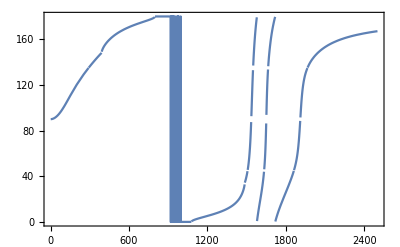

```mathematica
Plot[90*phaseShift[0.7,0.7,0.7,0.7,0.7,0.7,1535,141,1650,126,1910,502,w^2]/Pi,{w,0,2500},Frame->True]
```

## Fit

The parameter in the model is branch ratio x_{i,l}, decay width Gamma_l, resonance mass M_l.
We use NonlinearModelFit to fit the phase shift data.

```mathematica
nlm = NonlinearModelFit[data,90*phaseShift[x11,x12,x21,x22,x31,x32,m1,gamma1,m2,gamma2,m3,gamma3,w^2]/Pi,{{x11,0.7},{x12,0.7},{x21,0.7},{x22,0.7},{x31,0.7},{x32,0.7},{m1,1535},gamma1,{m2,1650},gamma2,{m3,1910},gamma3},w]
```

Inverse::luc: 病态矩阵 {{1.-5.02777×10^7 ⅈ,2.40106×10^11-2.40106×10^11 ⅈ},{2.40106×10^11-2.40106×10^11 ⅈ,2.29382×10^15-0.25 ⅈ}} 构成的 Inverse 的结果可能包含明显的数值错误.

Inverse::luc: 病态矩阵 {{1.-6.1484×10^7 ⅈ,2.63388×10^11-2.63388×10^11 ⅈ},{2.63388×10^11-2.63388×10^11 ⅈ,2.25714×10^15+0. ⅈ}} 构成的 Inverse 的结果可能包含明显的数值错误.

Inverse::luc: 病态矩阵 {{1.-7.68933×10^7 ⅈ,2.90507×10^11-2.90507×10^11 ⅈ},{2.90507×10^11-2.90507×10^11 ⅈ,2.19559×10^15+0. ⅈ}} 构成的 Inverse 的结果可能包含明显的数值错误.

General::stop: 在本次计算中，Inverse::luc 的进一步输出将被抑制.

FittedModel[(90 If[Arg[(√((«22»-«8» ⅈ)-«1») «3» «1»)/(w^4 (-(«1»)/(«1»)+«1»))+(«1»)/(«1»)]≥0,«1»,2 π+«1»])/π]

Inverse::luc: 病态矩阵 {{17.6819+1.37304×10^17 ⅈ,67736.1+2.87491×10^20 ⅈ},{67736.1+2.87491×10^20 ⅈ,2.10617×10^8+6.02236×10^23 ⅈ}} 构成的 Inverse 的结果可能包含明显的数值错误.

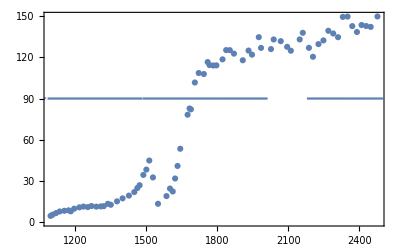

```mathematica
Show[ListPlot[data],Plot[nlm[x],{x,0,2500}],Frame->True]
```

```mathematica
nlm[1500]
```

```mathematica
nlm["ParameterConfidenceIntervalTable"]
```

Power::infy: 碰到无穷表达式 1/0..

General::stop: 在本次计算中，Power::infy 的进一步输出将被抑制.

Infinity::indet: 碰到不定表达式 0. ComplexInfinity.

General::stop: 在本次计算中，Infinity::indet 的进一步输出将被抑制.

| Estimate | Standard Error | Confidence Interval
x11 | 40863.8 | Indeterminate | {Indeterminate,Indeterminate}
x12 | 0.7 | Indeterminate | {Indeterminate,Indeterminate}
x21 | -32475.1 | Indeterminate | {Indeterminate,Indeterminate}
x22 | -66822. | Indeterminate | {Indeterminate,Indeterminate}
x31 | 41.3917 | Indeterminate | {Indeterminate,Indeterminate}
x32 | 144284. | Indeterminate | {Indeterminate,Indeterminate}
m1 | 664.983 | Indeterminate | {Indeterminate,Indeterminate}
gamma1 | -116861. | Indeterminate | {Indeterminate,Indeterminate}
m2 | -258.73 | Indeterminate | {Indeterminate,Indeterminate}
gamma2 | 92517.2 | Indeterminate | {Indeterminate,Indeterminate}
m3 | -5599.43 | Indeterminate | {Indeterminate,Indeterminate}
gamma3 | -146.09 | Indeterminate | {Indeterminate,Indeterminate}